```mathematica
str=Import["D:/1/vich lab/2/lab4/test1.txt","Table"];
data=Flatten[Table[{{(i-2)*str[[1,1]],(j-1)*str[[1,1]]},{str[[i,j]]}},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1];
fun=Interpolation[data];
Plot3D[fun[x,y],{x,0,1},{y,0,1}]
Graphics3D[{Red,,Axes->True,Point[Flatten[Table[{(i-2)*str[[1,1]],(j-1)*str[[1,1]],str[[i,j]]},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1]],PlotRange->{{-1,1},{-1,1},{-1,1}}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
str=Import["D:/1/vich lab/2/lab4/test2.txt","Table"];
data=Flatten[Table[{{(i-2)*str[[1,1]],(j-1)*str[[1,1]]},{str[[i,j]]}},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1];
fun=Interpolation[data];
Plot3D[fun[x,y],{x,0,1},{y,0,1}]
Graphics3D[{Red,,Axes->True,Point[Flatten[Table[{(i-2)*str[[1,1]],(j-1)*str[[1,1]],str[[i,j]]},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1]],PlotRange->{{-1,1},{-1,1},{-1,1}}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
str=Import["D:/1/vich lab/2/lab4/test3.txt","Table"];
data=Flatten[Table[{{(i-2)*str[[1,1]],(j-1)*str[[1,1]]},{str[[i,j]]}},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1];
fun=Interpolation[data];
Plot3D[fun[x,y],{x,0,1},{y,0,1}]
Graphics3D[{Red,,Axes->True,Point[Flatten[Table[{(i-2)*str[[1,1]],(j-1)*str[[1,1]],str[[i,j]]},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1]],PlotRange->{{-1,1},{-1,1},{-1,1}}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[x^2+y^2,{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
str=Import["D:/1/vich lab/2/lab4/testv16.txt","Table"];
data=Flatten[Table[{{(i-2)*str[[1,1]],(j-1)*str[[1,1]]},{str[[i,j]]}},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1];
fun=Interpolation[data];
Plot3D[fun[x,y],{x,0,1},{y,0,2}]
Graphics3D[{Red,,Axes->True,Point[Flatten[Table[{(i-2)*str[[1,1]],(j-1)*str[[1,1]],str[[i,j]]},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1]],PlotRange->{{-4,4},{-4,4},{-4,4}}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
str=Import["D:/1/vich lab/2/lab4/testv5.txt","Table"];
data=Flatten[Table[{{(i-2)*str[[1,1]],(j-1)*str[[1,1]]},{str[[i,j]]}},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1];
fun=Interpolation[data];
Plot3D[fun[x,y],{x,0,π},{y,0,π}]
Graphics3D[{Red,,Axes->True,Point[Flatten[Table[{(i-2)*str[[1,1]],(j-1)*str[[1,1]],str[[i,j]]},{i,2,Length[str]},{j,1,Length[str[[i]]]}],1]],PlotRange->{{-1,1},{-1,1},{-1,1}}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
A={{1,0,0,1},{0,1,λ,0},{Cos[λ 5],Sin[λ 5],λ,1},{-λ Sin[λ 5],λ Cos[λ 5],1, 0}}
```

{{1,0,0,1},{0,1,λ,0},{Cos[5 λ],Sin[5 λ],λ,1},{-λ Sin[5 λ],λ Cos[5 λ],1,0}}

```mathematica
A//MatrixForm
```

(1 | 0 | 0 | 1
0 | 1 | λ | 0
Cos[5 λ] | Sin[5 λ] | λ | 1
-λ Sin[5 λ] | λ Cos[5 λ] | 1 | 0)

```mathematica
A=({{1, 0, 0, 1}, {0, λ, 1, 0}, {Cos[L λ], Sin[L λ], L, 1}, {-λ Sin[L λ], λ Cos[L λ], 1, 0}})
```

{{1,0,0,1},{0,λ,1,0},{Cos[L λ],Sin[L λ],L,1},{-λ Sin[L λ],λ Cos[L λ],1,0}}

```mathematica
HH=Det[A]
HH=Simplify[HH]
```

-λ+2 λ Cos[L λ]-λ Cos[L λ]^2+L λ^2 Sin[L λ]-λ Sin[L λ]^2

λ (-2+2 Cos[L λ]+L λ Sin[L λ])

-2 λ+2 λ Cos[5 λ]+5 λ^2 Cos[5 λ]+2 λ Sin[5 λ]-5 (1+λ^2) Sin[5 λ]

```mathematica
NSolve[Tan[x]-x==0,x,Reals]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-x+Tan[x]==0,x,ℝ]

```mathematica
NSolve[Tan[x]==x,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Tan[x]==x,x]

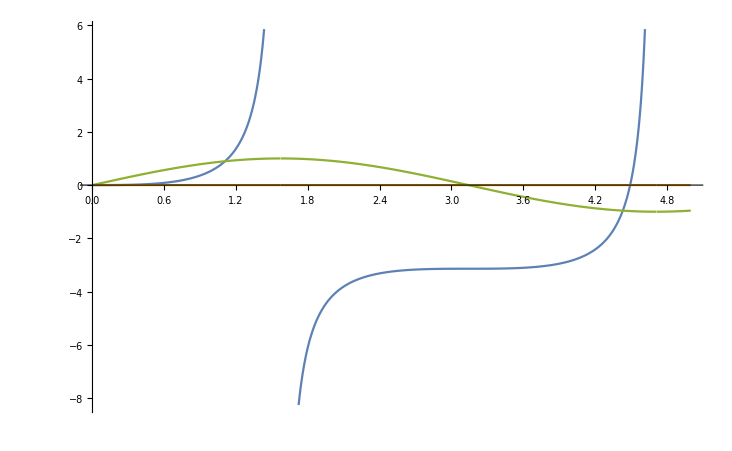

```mathematica
Plot[{Tan[x]-x,0,Sin[x]},{x,0,5}]
```

```mathematica
J={{1,0,0,1},{0,λ,1,0},{Cos[(λ L)/2]^2(1-λ^2/4),λ Cos[(λ L)/2]^2,L,1},{λ^2 Cos[(λ L)/2]^2,λ Cos[(λ L)/2]^2(1-λ^2/4),1,0}}
```

{{1,0,0,1},{0,λ,1,0},{(1-λ^2/4) Cos[(L λ)/2]^2,λ Cos[(L λ)/2]^2,L,1},{λ^2 Cos[(L λ)/2]^2,λ (1-λ^2/4) Cos[(L λ)/2]^2,1,0}}

```mathematica
J//MatrixForm
```

(1 | 0 | 0 | 1
0 | λ | 1 | 0
(1-λ^2/4) Cos[(L λ)/2]^2 | λ Cos[(L λ)/2]^2 | L | 1
λ^2 Cos[(L λ)/2]^2 | λ (1-λ^2/4) Cos[(L λ)/2]^2 | 1 | 0)

{{1,0,0,1},{0,λ,1,0},{Cos[L λ],1/2 L λ (1+Cos[L λ]),L,1},{-1/2 L λ^2 (1+Cos[L λ]),λ Cos[L λ],1,0}}

```mathematica
Det[J]
```

-λ+2 λ Cos[(L λ)/2]^2-1/2 λ^3 Cos[(L λ)/2]^2-L λ^3 Cos[(L λ)/2]^2-λ Cos[(L λ)/2]^4+3/2 λ^3 Cos[(L λ)/2]^4-1/16 λ^5 Cos[(L λ)/2]^4

```mathematica
Simplify[Det[J]]
```

-1/16 λ (16+8 (-4+(1+2 L) λ^2) Cos[(L λ)/2]^2+(16-24 λ^2+λ^4) Cos[(L λ)/2]^4)

```mathematica
j=4.4934094579090642
Tan[j]-j
```

4.49341

8.88178×10^-16

```mathematica
J={{1,0,0,1},{0,λ,1,0},{Cos[j]^2(1-λ^2/4),λ Cos[j]^2,L,1},{λ^2 Cos[j]^2,λ Cos[j]^2(1-λ^2/4),1,0}}
```

{{1,0,0,1},{0,λ,1,0},{0.0471904 (1-λ^2/4),0.0471904 λ,L,1},{0.0471904 λ^2,0.0471904 λ (1-λ^2/4),1,0}}

```mathematica
Det[J]
```

```mathematica
A=({{1, 0, 0, 1}, {0, λ, 1, 0}, {Cos[2 j], Sin[2 j], L, 1}, {-λ Sin[2 j], λ Cos[2 j], 1, 0}})
```

{{1,0,0,1},{0,λ,1,0},{-0.905619,0.424092,L,1},{-0.424092 λ,-0.905619 λ,1,0}}

```mathematica
Det[A]
```

```mathematica
-3.8112382030967655 λ+0.42409202174846444 2j λ
```

-1.07025×10^-13 λ